Needs::nocont: Context RootSearch` was not created when Needs was evaluated.

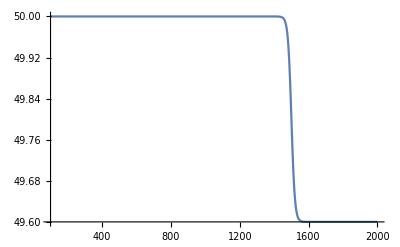

```mathematica
Needs["RootSearch`"]


fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals, FullSimplify@x]
myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;

CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 50;       (* dust kappa *)
TSUB =1500;

SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7/μm/.μm->1.;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;

MBH=10^7 Msol;

MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;

rulzGlob = {α->0.1, ϵ->0.1, η->0.1,  M->MBH, μ->1};
			
rulForConst={J->1, m->1,Rg->RGAS, σ->SGB, a->ARAD, G->Gr,c->CL, a->ARAD};

CalculateMdotNumber[rul_, excess_] := Module[{res},
	res =excess* μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul];
	

(*Dust opacity interpolation formuas*)

NKappa[t_,RadiusSwitch_:1.]:= Block[ {Ts = TSUB, ΔT=10, κ0=KPE, κ1=KPDUST},
			κ1 -RadiusSwitch*κ0(1+ Exp[-(t-Ts )/ΔT])^-1
];
Plot[NKappa[T],{T,100,2000}]
```

# StandDiskProps

Subroutine that calculates {TcRange, TsfRange, HeightRange, ρRange} as a function of input range of radii.

```mathematica
(* cell: cellNDiskTc *)

ClearAll[NSolve2LayerDisk, NSolveDisk,X,X1,EqTcSingleLayer,κ,r,T,
			NSolveDisk,NDiskTc,StandDiskProps,RWhereKappaCrosDustToGasSwitch]

RWhereKappaCrosDustToGasSwitch = 0;

StandDiskProps[R_, NMdot_:0.2MsolYr, Opac_, OmegaSlope_:1.5, R0_:0.01PC ] := Module[ {EqTc,Tsf,NSolvTc,FindSolForT, EqTcSingleLayer,Omega,HeightRange,HeightGasAndRad,MinTAtRadius,NTsurf, Tc,Fz, X1,KPD,Tsub,res,Tc1, NTc1,TcRange,TsfRange,minTAtRad,ΣColDens,ΣRange,ρRange,Pgas,Prad,HeightRad},
	
   KPD=KPDUST;
   Tsub=1500;

(*Print["Opac=",Opac];*)
(*Print["RWhereKappaCrosDustToGasSwitch = ",RWhereKappaCrosDustToGasSwitch];*)

 (*If[RWhereKappaCrosDustToGasSwitch<=0,
	RWhereKappaCrosDustToGasSwitch =1,
	RWhereKappaCrosDustToGasSwitch =1];
 *)

   Tsf[r_]:=((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)/.Mdt->NMdot/.rulForConst/.rulzGlob;

	Omega[r_] := Module[{Ω0 = G^(1/2) MBH^(1/2) R0^(-3/2)},(*Print@OmegaSlope;*)
					 Ω0(R0/r)^OmegaSlope]; 
	
		
	MinTAtRadius[r_]:=
Module[{eq,minT},minT=((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.κ->Opac[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;

eq[T_]:=(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2)+(J Mdt Ω)/(2 π T^4 α b))/.κ->Opac[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;

FindRoot[eq[T]==0,{T,10,minT}] 
							];
							
	minTAtRad=(MinTAtRadius[#]&/@ R)⟦All,1,2⟧;
	
   EqTcSingleLayer[T_,r_] := (-27 a^2 G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+
               16 σ (3 G^(3/2) J^2 m M^(3/2) Mdt^2 κ - 64 π^2 r^(9/2) Rg T^5 α σ)^2)/.κ->Opac[T]/.rulForConst/.rulzGlob/.Mdt->NMdot;
               
	HeightGasAndRad[r_,T_] :=(-(32 π Rg T σ)/(3 J m Mdt κ b  Ω^2) + (J Mdt Ω)/(2 π T^4 α b))/.κ->Opac[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;
                          
  HeightRad[r_,T_] := 3/(8 Pi) NMdot/CL Opac[T];
	
	TcRange=(MapThread[Quiet[FindRoot[EqTcSingleLayer[T,#1],{T,1,#2}]]&,{R,minTAtRad}])⟦All,1,2⟧;			 
	
	(*HeightRange = MapThread[HeightGasAndRad[#1,#2]&, {R,TcRange}];*)
	
	HeightRange = MapThread[HeightRad[#1,#2]&, {R,TcRange}];
	
	TsfRange = Tsf[#]&/@ R;

ΣColDens[r_,T_]:=(64 π T^4 σ)/(9 J Mdt κ Ω^2)/.κ->Opac[T]/.Ω->Omega[r]/.b->ARAD/.rulForConst/.rulzGlob/.Mdt->NMdot;
	
 ΣRange=MapThread[ΣColDens[#1,#2]&,  {R,TcRange}];
 ρRange = (ΣRange/(2 HeightRange))(* ⟦1⟧ *);
	
(*Print["ρRange=", ρRange];*)
	
{TcRange, TsfRange, HeightRange,ρRange}
					 
];

;
```

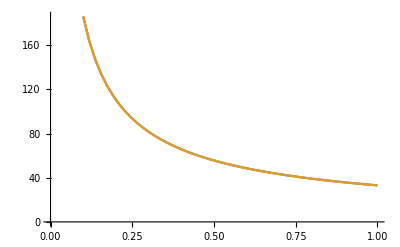

```mathematica
(*For different  Ω -slopes*)

ClearAll[Tc,Tsf,TcOmegaSlope,p1,p2];

RWhereKappaCrosDustToGasSwitch = 0;

xmin=0.1; xmax=1; Nx1=50;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

TcOmegaSlope =  Quiet@StandDiskProps[ PC X1, 0.2MsolYr, KPDUST, #]⟦2⟧ &/@ {1.5,1};

Append[p1, #]&/@( MapThread[{#1,#2}&, {X1, TcOmegaSlope⟦1⟧}]);

p1=MapThread[{#1,#2}&, {X1, TcOmegaSlope⟦1⟧}];
p2=MapThread[{#1,#2}&, {X1, TcOmegaSlope⟦2⟧}];

ListPlot[{p1,p2}, Joined->True]
```

## TcConvectiveDisk and others

RocConv ={1.00613×10^-12,1.83906×10^-12,2.82425×10^-12,3.941×10^-12,5.17531×10^-12,6.5169×10^-12,7.95779×10^-12,9.49154×10^-12,1.11129×10^-11,1.28172×10^-11,1.46008×10^-11,1.64602×10^-11,1.83924×10^-11,2.03948×10^-11,2.24651×10^-11,2.4601×10^-11,2.68006×10^-11,2.90621×10^-11,3.13839×10^-11,3.37644×10^-11,3.62023×10^-11,3.86961×10^-11,4.12447×10^-11,4.38469×10^-11,4.65017×10^-11,4.9208×10^-11,5.19648×10^-11,5.47713×10^-11,5.76265×10^-11,6.05297×10^-11,6.34801×10^-11,6.6477×10^-11,6.95195×10^-11,7.26071×10^-11,7.57392×10^-11,7.8915×10^-11,8.21339×10^-11,8.53956×10^-11,8.86992×10^-11,9.20444×10^-11,9.54307×10^-11,9.88574×10^-11,1.02324×10^-10,1.05831×10^-10,1.09376×10^-10,1.12961×10^-10,1.16583×10^-10,1.20244×10^-10,1.23942×10^-10,1.27677×10^-10,1.31449×10^-10,1.35258×10^-10,1.39102×10^-10,1.42983×10^-10,1.46898×10^-10,1.50849×10^-10,1.54835×10^-10,1.58855×10^-10,1.62909×10^-10,1.66998×10^-10,1.71119×10^-10,1.75275×10^-10,1.79463×10^-10,1.83684×10^-10,1.87938×10^-10,1.92224×10^-10,1.96542×10^-10,2.00893×10^-10,2.05274×10^-10,2.09687×10^-10,2.14132×10^-10,2.18607×10^-10,2.23113×10^-10,2.27649×10^-10,2.32216×10^-10,2.36813×10^-10,2.4144×10^-10,2.46097×10^-10,2.50783×10^-10,2.55499×10^-10,2.60244×10^-10,2.65018×10^-10,2.6982×10^-10,2.74652×10^-10,2.79512×10^-10,2.844×10^-10,2.89316×10^-10,2.9426×10^-10,2.99233×10^-10,3.04233×10^-10,3.0926×10^-10,3.14315×10^-10,3.19397×10^-10,3.24506×10^-10,3.29642×10^-10,3.34805×10^-10,3.39995×10^-10,3.45211×10^-10,3.50454×10^-10,3.55722×10^-10}

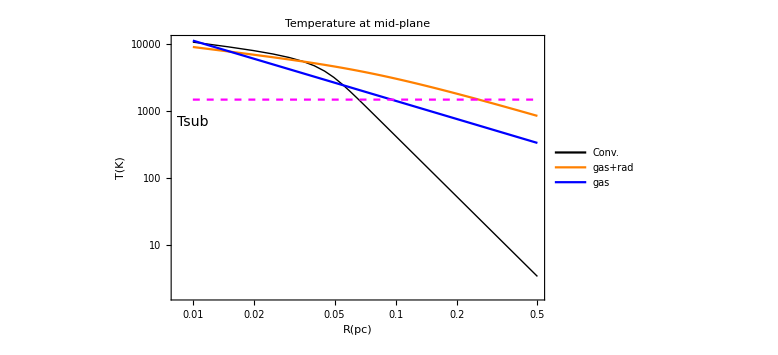

```mathematica
(*run cell:cellStandDiskProps before*)

ClearAll[TcGasDisk,TcConvectiveDisk,TcConvectiveDiskWithBeta,RocConvectiveDisk,HeightGasAndRad, Tconv2Tgas,Mdt,Mdt1, TcConv, Tc,Tsf,Hc, β]
ClearAll[Tsf,TcMat,TsfMat,MdotRange,lenTc,rTc,rTsf,Nmdot,MdotMin,MdotMax,pltIn,pltOut,pltHeightOut,hRc1,HeightRad,plotDiskTemp,RocConv];
ClearAll[Mdot,Tsub];

TcGasDisk[r_, Mt_,Opac_] := (((3/2)^(1/5) J^(2/5) m^(1/5) (Mt)^(2/5) (κ)^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5)))/.{σ->a c/4, Ω->(G M /r^3)^(1/2),κ->Opac}/.rulForConst/.rulzGlob;



TcConvectiveDiskWithBeta[r_, κ_,α_,M_,β_] := ((1-β)/(3a)Ω c/κ)^(1/4)/.Ω->(G M /r^3)^(1/2)/.rulForConst;


RocConvectiveDisk[r_, κ_,α_,M_,β_,Mt_]:= Module[{K,zb, μ=1},
				K= ((3 RGAS^4)/(ARAD μ^4))^(1/3)((1-β)/β^4)^(1/3);
				zb=3/(8 Pi) Mt/CL κ;
				(Ω^2/(8K))^3((3Mt κ)/(8Pi c))^6/.Ω->(G M /r^3)^(1/2)/.rulForConst
				]
				
(*RocConvectiveDisk[0.1PC Subscript[r, 0.5], 50 Subscript[κ, 50],0.1α01,10^7 Msol Subscript[M, 7],0.5,0.1MsolYr];*)

TcConvectiveDisk[r_,Mt_,  Opac_, dbg_:False,β_:0.5]:= 
Module[{K,zb, μ=1,Ω,A1,A0,κ,roc, Tc, Trc, Pc},
					κ=Opac[Tc,1];
					(*κ=KPDUST;*)
					(*Print["κ=", Opac];*)
					Ω=(G M /r^3)^(1/2);
					K= ((3 RGAS^4)/(ARAD μ^4))^(1/3)((1-β)/β^4)^(1/3);
					zb=3/(8 Pi) Mt/CL κ;
					(*roc = (Ω^2/(8K)zb^2)^3/.rulForConst/.rulzGlob;*)
					roc = ((9 κ α Ω)/(64CL)zb^2)^-1/.rulForConst/.rulzGlob;
					A1 = (3RGAS)/ARAD roc/.rulForConst/.rulzGlob;
					A0 = (24 Ω CL)/(9ARAD κ α)/.rulForConst/.rulzGlob;
					Trc=((24Ω CL)/(9ARAD κ α) )^(1/4)/.rulForConst/.rulzGlob;
									
					Tc = FindRoot[T^4+A1 T - A0 ==0,{T,1,10000}]⟦1⟧⟦2⟧;
					(*Print["Tc in=",Tc];*)

(*If[dbg==True, Print["Pg = ", roc RGAS Trc,"\n",  
"Pr = " , ARAD Trc^4/3,"\n", "roc=", roc,  "\n",  "A0=", A0, "\n","A1=",A1, "\n", 
"Tc = ",Tc,"\n","Trc = ", Trc], Tc]*)

{Tc,roc}
]

xmin=0.01; xmax=0.5; Nx1=100;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

Mdot= 0.2MsolYr;
Tsub = 1500;

{Tc, Tsf, Hc, rhoc} = (*Quiet@*) StandDiskProps[ PC X1, Mdot,(KPDUST&), 1.5];
(*Print["Tc=",Tc];*)
(*ListLogLogPlot[MapThread[{#1,#2}&, {X1, Tc}];*)

TsubLine = MapThread[{#1, #2}&,  {X1, Table[Tsub, {i, Nx1}]}];
(*TcConv= Quiet@TcConvectiveDisk[PC X1,Mdot,(KPDUST&)];*)

res= Quiet@TcConvectiveDisk[#,Mdot,(KPDUST&)]&/@ (PC X1);
TcConv =res⟦All,1⟧;
RocConv =res⟦All,2⟧;

Print["RocConv =",RocConv ]

p1=MapThread[{#1,#2}&, {X1, TcConv}];
p2 =MapThread[{#1,#2}&, {X1, Tc}];
p3=MapThread[{#1,#2}&, {X1, (TcGasDisk[#, Mdot,KPE] &/@ (PC X1)) }];

plotDiskTemp=Module[{thisPlotSize=14},
    ListLogLogPlot[{p1,p2,p3,TsubLine}, Joined->True,Frame->True,
PlotStyle->{{Thick,Black}, Orange,Blue, {Magenta,Dashed}},
PlotLabel->Style["Temperature at mid-plane",Black,thisPlotSize],
FrameLabel->{Style["R(pc)",Black,thisPlotSize], Style["T(K)",Black,thisPlotSize]},
PlotLabels->{"","","",Placed[Style["Tsub",thisPlotSize],Left]},
PlotLegends->Placed[LineLegend[{"Conv.","gas+rad","gas" },LegendFunction->Framed],{0.12,0.2}],
ImageSize->Large
]
]

(*Export["/Users/dora/Documents/TEX/torus10/RadDiskTemp.pdf", plotDiskTemp]*)

ClearAll[Tsf,TcMat,TsfMat,MdotRange,lenTc,rTc,rTsf,Nmdot,MdotMin,MdotMax,pltIn,pltOut,pltHeightOut,hRc1,HeightRad,plotDiskTemp];
ClearAll[Mdot,Tsub]
```

```mathematica
TcConv//Dimensions

TcConv[[1;;2]]//MatrixForm

TcConv⟦All,1⟧
```

{100,2}

(10847. | 1.00613×10^-12
9215.37 | 1.83906×10^-12)

{10847.,9215.37,8100.58,7202.19,6393.4,5607.23,4808.63,3997.14,3218.29,2540.82,2000.72,1588.69,1277.44,1040.73,858.462,716.154,603.547,513.324,440.208,380.336,330.844,289.578,254.898,225.541,200.525,179.075,160.579,144.544,130.576,118.35,107.605,98.1217,89.721,82.2525,75.5904,69.6288,64.278,59.4617,55.1148,51.1815,47.6137,44.37,41.4143,38.7155,36.2461,33.9824,31.9033,29.9904,28.2274,26.6,25.0952,23.7019,22.4099,21.21,20.0943,19.0556,18.0872,17.1833,16.3386,15.5485,14.8084,14.1146,13.4635,12.8518,12.2766,11.7352,11.2252,10.7444,10.2906,9.86196,9.45684,9.07361,8.71081,8.36709,8.04122,7.73206,7.43855,7.1597,6.89462,6.64247,6.40246,6.17388,5.95605,5.74835,5.5502,5.36104,5.18039,5.00777,4.84273,4.68486,4.53378,4.38913,4.25056,4.11777,3.99045,3.86833,3.75114,3.63864,3.53059,3.42677}

```mathematica
(*xmin=0.01; xmax=0.5; Nx1=10;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

TcConvectiveDisk[0.05PC,0.2MsolYr]

Mdot= 0.2MsolYr;
Tsub = 1500;

SolveDiskOnStichRGridForTwoKappad[X_] := Module[{res},
 

{Tc, Tsf, Hc, rhoc} = (*Quiet@*) StandDiskProps[ PC X, Mdot, KPDUST, 1.5];

Print[Tc];
For[i=1,i<=Length[X],i++, Print[X⟦i⟧ ]]

]

SolveDiskOnStichRGridForTwoKappad[X1] *)
```

/Users/dora/Documents/TEX/torus10/RadDiskTemp.pdf

```mathematica
ClearAll[GetConvectiveFlux];

GetConvectiveFlux[ρ_,T_,x_,z_,NMdot_:0.2MsolYr,Opac_] :=Module[{Prad,Pgas,KPD,Tsub,Cp,
	dTdzRad,dTdzAdiab,GradConv,dTdzRadRange,dTdzAdiabRange,GradConvRange,ConvectiveFlux,RadiationFlux,RadiationFluxFromViscDiss,CppltFlxRatio, tmp},

KPD=KPDUST;
Tsub=1500; 

Prad= (ARAD/3) T^4;	
     Pgas= RGAS ρ T;


dTdzRad[ρi_, Ti_, ri_] := Module[{Fz,Mdt=NMdot,Ω=G^(1/2) MBH^(1/2) ri^(-3/2),κ=Opac[Ti]},
Fz=3/8 Mdt  Ω^2;
-(3 κ ρi Fz)/(4 ARAD CL Ti^3) /.rulForConst];
    


dTdzRadRange = MapThread[dTdzRad[#1, #2, #3]&,{ρ,T,x}];

dTdzAdiab[ρi_, Ti_,ri_,zi_] := Module[{gradAd,β,Mdt=NMdot,g,Ω=G^(1/2) MBH^(1/2) ri^(-3/2)},
	β = (RGAS ρi Ti)/((ARAD/3) Ti^4+RGAS ρi Ti);
	gradAd = (1+((4+β)(1-β))/β^2)/(5/2+(4(4+β)(1-β))/β^2);
	g=Ω^2 zi;
	-g ρi Ti/((ARAD/3) Ti^4+RGAS ρi Ti) gradAd /.rulForConst
];

dTdzAdiabRange = MapThread[dTdzAdiab[#1, #2, #3,#4]&,{ρ,T,x,z} ];

tmp =-dTdzRadRange + dTdzAdiabRange; (*because dT/dx_rad is negative*)
(*Print[tmp];*)

GradConvRange=If[#<0, 0, #] &/@ Flatten[tmp];(*Flatten[(Abs[dTdzRadRange ]-Abs[dTdzAdiabRange])];*)


Cp = RGAS(5./2. + (20.Prad)/Pgas + ((4Prad)/Pgas)^2);
(*Print[ρ,T,x,z];
Print["\n Length[dTdzRadRange] =", Length[dTdzRadRange] ];
Print["\n Length[dTdzAdiabRange] =", Length[dTdzAdiabRange] ];
Print[Length[(Abs[dTdzRadRange ]-Abs[dTdzAdiabRange])]];
Print["dTdzRadRange=",dTdzRadRange,Length[dTdzRadRange]
, "\n dTdzAdiabRange=",dTdzAdiabRange,
"\n diff=", (dTdzRadRange-dTdzAdiabRange),
"\n GradConvRange=",GradConvRange, 
"\n Cp=",Cp
];
*)
(*Print["\n",Length[GradConvRange],"\n",Length[ρ],"\n",Length[x],"\n",Length[z]];*)

ConvectiveFlux=Block[
{Ω=G^(1/2) MBH^(1/2) x^(-3/2),mixLen=0.1z},(Cp ρ ((Ω^2 z)/T)^(1/2)GradConvRange)mixLen^2/4.(*(1. + (4.Prad)/Pgas)^(1/2)*) /.rulForConst];


(*Print["ConvectiveFlux=",ConvectiveFlux];*)
(*(*ConvectiveFlux=If[#>Tsub, 0, ConvectiveFlux]& /@ T;*)*)

RadiationFluxFromViscDiss=Block[{Ω=G^(1/2) MBH^(1/2) x^(-3/2)},3/8 Mdt  Ω^2 /.rulForConst/.Mdt->NMdot];

RadiationFlux = -(4 ARAD CL)/3 dTdzRadRange MapThread[ #2^3/(Opac[#2] #1)&,{ρ,T}];


{
ConvectiveFlux,
RadiationFlux(*,
dTdzRadRange,
dTdzAdiabRange*)
}
(*FconvEq = Cp ρ (g/T)^(1/2)(ΔT)^(3/2) l^2/4 (1 + (4Pr)/Pg)^(1/2);*)
]



(*ConvectiveFlux/RadiationFlux*)
(*uncom pltFlxRatio = (*ListLog*)Plot[ MapThread[{#1,#2}&, {X1, ConvectiveFlux}], Joined->True]*)
(*/RadiationFlux*)
(*ConvectiveFlux=If[#>Tsub, 0, ConvectiveFlux]& /@ T;*)
(*{pltFlxRat,pltT}*)
(*ClearAll[ρc,Tc,X1,GetConvectiveFlux];*)
(*ClearAll[ConvectiveFlux, RadiationFlux]*)
```

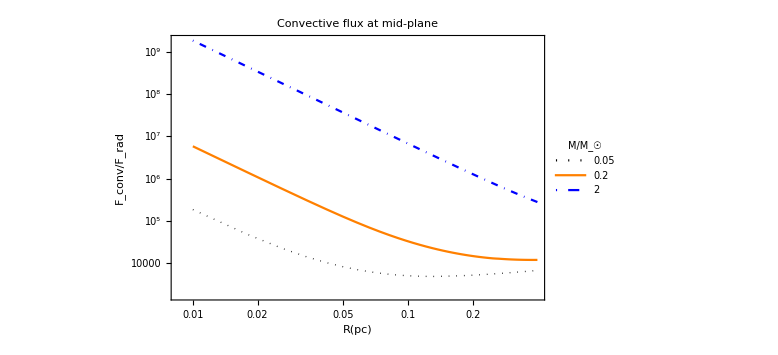

```mathematica
(*Calculate and plot convective/radiation flux*)

ClearAll[ConvectiveFlux,RadiationFlux,MdotRangeInMSolYr,plt, MdotRange,MdotRangeStr,X1,Tc,Tsf,Hc,ρc]

xmin=0.01; xmax=0.4; Nx1=50;
X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

MdotRangeInMSolYr= {0.05, 0.2, 2};

(*MdotRangeStr=ToString[MdotRange]*)

MdotRange= MsolYr MdotRangeInMSolYr;

Tsub = 1500;

plt={};

For[i=1,i<=Length[MdotRange],i++, 

Mdot=MdotRange⟦i⟧;
(*Print["\n Mdot=",Mdot];*)

{Tc, Tsf, Hc,ρc}=Quiet@StandDiskProps[PC X1, Mdot,KPDUST&, 1.5, 0.01PC];

(*TcConv = Quiet@TcConvectiveDisk[#,Mdot,(KPDUST&)]&/@ (PC X1);*)
(*TcConv = Quiet@TcConvectiveDisk[PC X1,Mdot,(KPDUST&)];*)
(*Print[TcConv];*)
(*RocConv= RocConvectiveDisk[r_, κ_,0.1,MBH,β_,Mt_];*)


{ConvectiveFlux, RadiationFlux} = (*Quiet@*)GetConvectiveFlux[ρc, Tc, PC X1, Hc,Mdot,NKappa];
(*ConvectiveFlux*)

p1=MapThread[{#1,#2}&, {X1, ConvectiveFlux/RadiationFlux}];
plt=Append[plt, p1];

]
plotConvToRadFLux=Module[{thisPlotSize=14},
    ListLogLogPlot[plt, Joined->True,Frame->True,
PlotStyle->{{Thick,Black,Dotted}, Orange,{Blue,DotDashed}},

PlotLabel->Style["Convective flux at mid-plane",Black,thisPlotSize],

FrameLabel->{Style["R(pc)",Black,thisPlotSize], Style["F_conv/F_rad",Black,thisPlotSize]},

(*PlotLabels->{"","","",Placed[Style["Tsub",thisPlotSize],Left]},*)

PlotLegends->Placed[LineLegend[MdotRangeInMSolYr, LegendLabel->"Ṁ/M_☉",LegendFunction->Framed],{0.8,0.8}],

ImageSize->Large
]
]

(*Export["/Users/dora/Documents/TEX/torus10/plotConvToRadFLux.pdf",plotConvToRadFLux]*)
```

# Estimations of F_conv

Stability condition:

```mathematica
Assuming[{r>0,Ω>0∧J>0∧ m>0∧Mdt>0∧Rg>0∧OneMinB>0∧α>0∧κ>0∧σ>0∧M>0∧Ts>0 ∧G>0∧ Mdt>0},
FullSimplify[(3^(1/10) J^(1/5) m^(3/5) (√G √M)^(7/10) Mdt^(1/5) κ^(1/10) Ω^(3/5))/(2^(3/5) π^(1/5) r^(1/20) Rg^(3/5) α^(1/10) σ^(1/10))/.Ω->(G M /r^3)^(1/2)]];


ClearAll[TcToZ,TcGasOnlyDisk];


TcGasOnlyDisk[r_,Mdt_,κ_]:= ((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.Ω->(G M /r^3)^(1/2);
HcGasOnlyDisk[r_,Mdt_,κ_]:= (3^(1/10) J^(1/5) Mdt^(1/5) Rg^(2/5) κ^(1/10))/(2^(3/5) m^(2/5) π^(1/5) ((√G √M)/r^(3/2))^(7/10) α^(1/10) σ^(1/10))/.M->MBH/.rulForConst/.rulzGlob;

TcToZ[r_,Mdt_] := Module[{Ω,res,Ts,Tc,Hc},
Ω=(G M /r^3)^(1/2);

Ts = ((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4);

Hc=HcGasOnlyDisk[r,Mdt,KPDUST];

Print[" (H)_gas = ",  Hc/.M->MBH/.rulForConst/.rulzGlob];

Tc=TcGasOnlyDisk[r,Mdt,KPDUST];

(Ts-Tc)/Hc/.M->MBH/.rulForConst/.rulzGlob

];

Print[" (dT/dz)_gas ≂ T_c/h= ",(* TcToZ[r,Mdt]*)TcToZ[0.1PC,0.2MsolYr] ]
```

(H)_gas = 2.63676×10^15

(dT/dz)_gas ≂ T_c/h= -1.3622×10^-12

```mathematica
ClearAll[ConvectionEstimate];

ConvectionEstimate[n0_,T_,x_,z_,Mdt_,Opac_:KPDUST ]:=Module[
{Prad,Pgas,KPD,Tsub,Cp,Ω=G^(1/2) MBH^(1/2) x^(-3/2),mixLen=ϵ01 0.1z ,
DtConv,EnergyFlux,p1,dTdzRad,dTdzAdEst,ρ,T0=1500,β,gradAd},

ρ=n0 MP;
Prad= (ARAD/3) T^4;	
     Pgas= RGAS ρ T;
β=Pg/(Pr+Pg);
Cp = RGAS(5./2. + (20.Prad)/Pgas + ((4Prad)/Pgas)^2);
gradAd= (1+((4+β)(1-β))/β^2)/(5/2+(4(4+β)(1-β))/β^2);

EnergyFlux = 3/(8π)Mdt Ω^2;

dTdzRad= (-3Opac MP n0)/(4ARAD CL T0^3)EnergyFlux/.rulForConst;

Print["dTdzRad = ", dTdzRad];
Print["dTdzAdEst = ", dTdzAdEst = -T0/(Prad+Pgas)Ω^2 z ρ/.rulForConst];
Print["dTdzAdiab = ", -T0/(Prad+Pgas)Ω^2 z ρ/.rulForConst];

p1=(1. + (4.Prad)/Pgas)^(1/2); p1=1;
DtConv=EnergyFlux( (Cp ρ ((Ω^2 z)/T)^(1/2))mixLen^2/4. p1 )^-1/.rulzGlob/.rulForConst;
DtConv^(2/3)

]


ClearAll[GetStandardDiskAsInerpolatedFuncions,Tc,nc,Hc,Mdot0, Tref];

GetStandardDiskAsInerpolatedFuncions[Mdot_]:=  
Module[{xmin=0.01, xmax=0.5, Nx1=100,Tc, Tsf, Hc, ρc,nc},

  X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

{Tc, Tsf, Hc, ρc} = Quiet@ StandDiskProps[ PC X1, Mdot,(KPDUST&), 1.5];(*Print[ρc];*)
Tc = Quiet@ListInterpolation[Tc, X1];
nc = Quiet@ListInterpolation[ρc MP^-1, X1];
Hc = Quiet@ListInterpolation[Hc, X1];
{Tc,nc,Hc}
]

Mdot0 = 0.2MsolYr;
Tref = 1500;

{Tc,nc,Hc} = GetStandardDiskAsInerpolatedFuncions[Mdot0];

xc = Solve[Tc[x]==Tref,x]⟦1,1,2⟧


Module[{r,n, Mdt=Mdot0,Tc,Hgas,T=Tref},

r=xc PC;
 n=nc[xc];
(*Print[xc,"\n",n];*)

Hgas=HcGasOnlyDisk[r,Mdt,KPDUST];
Echo[Hgas,"Hgas="];Echo[n,"n ="];
(*Tc=TcGasOnlyDisk[r,Mdt,KPDUST];*)

ConvectionEstimate[n,T, r, Hgas,Mdt ]

]
```

0.257395

Hgas= 7.11542×10^15

n = 4.57024×10^11

dTdzRad = -1.49328×10^-13

dTdzAdEst = -1.99944×10^-13

dTdzAdiab = -1.99944×10^-13

8.68486×10^-13 (1/ϵ01^2)^(2/3)

Set::shape: Lists {Tc,nc} and {«1»} are not the same shape.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Tc^(-1)[1000]}}

Tc^(-1)[1000]

```mathematica
((-27 a^2 G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+
               16 σ (3 G^(3/2) J^2 m M^(3/2) Mdt^2 κ - 64 π^2 r^(9/2) Rg T^5 α σ)^2)/.{σ.00->a c/4,Mdt->Ṁ})/a//FullSimplify
C1 = Coefficient[%,T,0]
```

-27 a G^(5/2) J^4 m^2 M^(5/2) r^(3/2) T^4 α κ^3 (Ṁ)^4+4 c (16 a c π^2 r^(9/2) Rg T^5 α-3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)^2

```mathematica
-27 a G^(5/2) J^4 m^2 M^(5/2) r^(3/2) T^4 α κ^3 (Ṁ)^4/(4c(3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)^2)//Simplify
```

-(3 a r^(3/2) T^4 α κ)/(4 c √G √M)

```mathematica
16 a c π^2 r^(9/2) Rg T^5 α/(3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)//Simplify
```

(16 a c π^2 r^(9/2) Rg T^5 α)/(3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)

```mathematica
(16 a c π^2 r^(9/2) Rg T^5 α)/(3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)
```

```mathematica
Assuming[{Ω>0 && G>0 &&M>0},Simplify[(16 a c π^2 r^(9/2) Rg T^5 α)/(3 G^(3/2) J^2 m M^(3/2) κ (Ṁ)^2)/.r->(Ω^2/(G M))^(-1/3)/. Ṁ->SuperPlus[F] 8 π/3 Ω^-2 ]]
```

(3 a c Rg T^5 α Ω)/(4 J^2 m κ (F^+)^2)

## R_in, R_out (Ṁ), q-factors, plots:

```mathematica
Module[{
xmin=0.01, xmax=5, Nx1=100,Nmdot=10,
MinMdot = 0.01, MaxMdot   =4 ,X1,mdtRange,Tc,Tsf,Hc,rhoc,
rcRange,rsRange},

X1 =  Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];

mdtRange =  Range[MinMdot,MaxMdot ,(MaxMdot-MinMdot)/(Nmdot-1) ];

rcRange = Table[0, {i,1,Nmdot}];
rsRange = Table[0, {i,1,Nmdot}];

Module[{M},
For[i=1,i≤Nmdot,i++, 
M=MBH;
{Tc, Tsf, Hc, rhoc} = (*Quiet@*) StandDiskProps[ PC X1, MsolYr*mdtRange⟦i⟧,(KPDUST&), 1.5];
Tc = Quiet@ListInterpolation[Tc, X1];

rcRange⟦i⟧ = Quiet@Solve[Tc[x]==TSUB,x]⟦1,1,2⟧;

rsRange⟦i⟧ = (G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 TSUB^(4/3) σ^(1/3))/.Mdt->MsolYr*mdtRange⟦i⟧/.rulForConst;

Print[rcRange⟦i⟧,"  ", rsRange⟦i⟧/PC, "  ", mdtRange⟦i⟧];
]];

ListPlot[rcRange, mdtRange]

]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

0.0660378  0.00227947  0.01

0.359458  0.00812782  0.453333

0.470236  0.0102026  0.896667

0.54759  0.0116646  1.34

0.608119  0.0128306  1.78333

0.658103  0.0138161  2.22667

0.700721  0.0146782  2.67

0.737838  0.0154493  3.11333

0.770655  0.0161504  3.55667

0.799997  0.0167953  4.

ListPlot::nonopt: Options expected (instead of {0.01,0.453333,0.896667,1.34,1.78333,2.22667,2.67,3.11333,3.55667,4.}) beyond position 1 in ListPlot[{0.0660378,0.359458,0.470236,0.54759,0.608119,0.658103,0.700721,0.737838,0.770655,0.799997},{0.01,0.453333,«6»,3.55667,4.}]. An option must be a rule or a list of rules.

ListPlot[{0.0660378,0.359458,0.470236,0.54759,0.608119,0.658103,0.700721,0.737838,0.770655,0.799997},{0.01,0.453333,0.896667,1.34,1.78333,2.22667,2.67,3.11333,3.55667,4.}]

```mathematica
(*MidDiskSubRadRadius[M_,Mdt_] := (G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3));
SurfDiskSubRadRadius


MdotRange = (FOut[#,par]&)/@ mdtRange;
ToPlot =MapThread[{#1,#2}&, {mdtRange,MdotRange}];

	ListPlot[ ToPlot,Joined->True,Frame->True,AspectRatio->Full]*)
	






FilterRules[rulzGlobWithScales,M]
{M->1.9890000000000002*^40 Subscript[M, 7]}
```